```mathematica
RandomReal[]
```

0.893612

```mathematica
IntegerPart[0.8936120036978057]
```

0

```mathematica
list=Table[0,{i,100000}];
For[i=1,i<50001,i++,{
x1=RandomReal[],
x2=RandomReal[],
rho=-2*Log[x2],
omega=2*Pi*x1,
list[[i]]=Sqrt[rho]*Cos[omega],
list[[i+50000]]=Sqrt[rho]*Sin[omega]}]
```

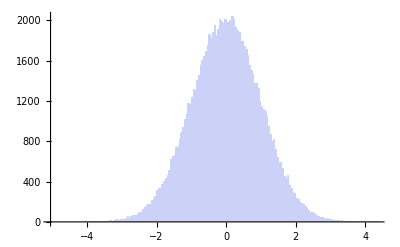

```mathematica
Histogram[list]
```

```mathematica
Eigenvalues[({{1, 0, 0, 0, 0}, {0, 1, 2, 3, 0}, {0, 4, 5, 6, 0}, {0, 7, 8, 9, 0}, {0, 0, 0, 0, 1}})]//N
```

{16.1168,-1.11684,1.,1.,0.}

{{1,2,3},{4,5,6},{7,8,9}}

```mathematica
M1[T_]:=({{Cos[T], Sin[T], 0}, {-Sin[T], Cos[T], 0}, {0, 0, 1}})
M1T[T_]:=Transpose[({{Cos[T], Sin[T], 0}, {-Sin[T], Cos[T], 0}, {0, 0, 1}})]
M2[T_]:=({{1, 0, 0}, {0, Cos[T], Sin[T]}, {0, -Sin[T], Cos[T]}})
M2T[T_]:=Transpose[({{1, 0, 0}, {0, Cos[T], Sin[T]}, {0, -Sin[T], Cos[T]}})]
M3[T_]:=({{1, 0, 0, 0, Sin[T]}, {0, Cos[T], 0, 0, 0}, {0, 0, 0, 0, 0}, {0, 0, 0, 0, 0}, {0, -Sin[T], 0, 0, Cos[T]}})
M3T[T_]:=Transpose[({{1, 0, 0, 0, Sin[T]}, {0, Cos[T], 0, 0, 0}, {0, 0, 0, 0, 0}, {0, 0, 0, 0, 0}, {0, -Sin[T], 0, 0, Cos[T]}})]
```

```mathematica
M=M2=({{1, 1, 1}, {0.01, 0, 0.01}, {0., 0.01, 0.01}})
```

{{1,1,1},{0.01,0,0.01},{0.,0.01,0.01}}

```mathematica
i=3;
j=2;
MGivens=({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}});
MGivens[[i,i]]=M[[j,j]]/Sqrt[M[[j,j]]^2+M[[i,j]]^2];
MGivens[[j,j]]=M[[j,j]]/Sqrt[M[[j,j]]^2+M[[i,j]]^2];
MGivens[[i,j]]=-M[[i,j]]/Sqrt[M[[j,j]]^2+M[[i,j]]^2];
MGivens[[j,i]]=M[[i,j]]/Sqrt[M[[j,j]]^2+M[[i,j]]^2];
M=MGivens.M//N
```

{{1.00005,0.99995,1.00005},{0.,0.0141418,0.00707124},{0.,0.,-0.00707089}}

```mathematica
M//MatrixForm
```

(1.00005 | 0.99995 | 1.00005
0. | 0.0141418 | 0.00707124
0. | 0. | -0.00707089)

```mathematica
MGivens2=MGivens
```

{{0.99995,0.0099995,0},{-0.0099995,0.99995,0},{0,0,1}}

```mathematica
MGivens3=MGivens
```

{{1.,0,0.},{0,1,0},{0.,0,1.}}

```mathematica
MGivens4=MGivens
```

{{1,0,0},{0,-0.707089,0.707124},{0,-0.707124,-0.707089}}

```mathematica
Q=Transpose[MGivens2].Transpose[MGivens3].Transpose[MGivens4]
```

{{0.99995,0.00707054,0.00707089},{0.0099995,-0.707054,-0.707089},{0.,0.707124,-0.707089}}

```mathematica
Q.M//MatrixForm
```

(1. | 1. | 1.
0.01 | -1.73472×10^-18 | 0.01
0. | 0.01 | 0.01)

```mathematica
M.Q//MatrixForm
```

(1.01 | 0.0072123 | -1.40711
0.000141411 | -0.00499875 | -0.0149995
0. | -0.005 | 0.00499975)